```mathematica
μm=10^-6;
c=299792458;
fs=10^-15;
mm=10^-3;
nm=10^-9;
```

```mathematica
(*From QIOptiq internal comunication and also http://www.foctek.net/products/kdp_crystals.htm*)
no[λ_]:=(1.9575544+(0.2901391(λ/μm)^2)/((λ/μm)^2-0.0281399)-0.02824391(λ/μm)^2+0.004977826(λ/μm)^4)^(1/2)
ne[λ_]:=(1.5005779+(0.6276034(λ/μm)^2)/((λ/μm)^2-0.0131558)-0.01054063(λ/μm)^2+0.002243821(λ/μm)^4)^(1/2)
```

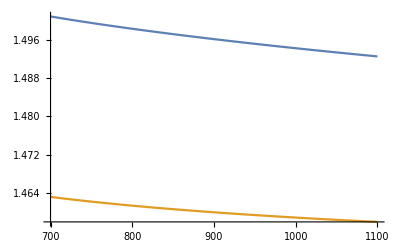

```mathematica
Plot[{no[λ nm],ne[λ nm]},{λ,700,1100}]
```

```mathematica
(*Group velocity dispersion (GVD). Ref: Young 2015 and Newport website*)
GVDo[λ_]:=(λ^3 no''[λ])/(2π c^2)
GVDe[λ_]:=(λ^3 ne''[λ])/(2π c^2)
(*Group delay dispersion (GDD = GVD*L, where L is the material thickness) vs wavelength*)
GDDo[L_,λ_]:=L*GVDo[λ]
GDDe[L_,λ_]:=L*GVDe[λ]
```

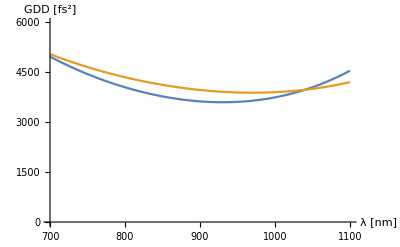

```mathematica
L=112mm;
Plot[{GDDo[L,λ nm]/fs^2,GDDe[L,λ nm]/fs^2},{λ,700,1100},PlotRange->{0,6000},AxesLabel->{"λ [nm]","GDD [fs^2]"}]
```

```mathematica
Δtout[Δt_,GDD_]:=(√(Δt^4+16 Log[2]^2 GDD^2))/Δt(*Gaussian pulse broadening*)
(*Ref: Eq8 in http://www.newport.com/The-Effect-of-Dispersion-on-Ultrashort-Pulses/602091/1033/content.aspx*)
```

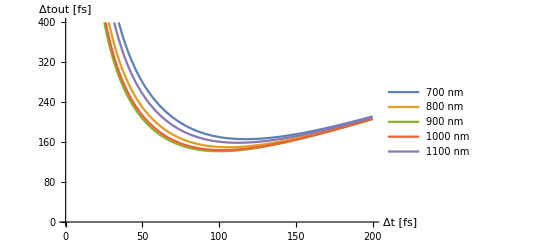

```mathematica
(*output pulsewidth vs input pulsewidth, gaussian pulses*)
Plot[Evaluate[Table[Δtout[Δt fs,GDDo[L,λ nm]]/fs,{λ,700,1100,100}]],{Δt,0,200},PlotRange->{0,400},AxesLabel->{"Δt [fs]","Δtout [fs]"},PlotLegends->{"700 nm","800 nm","900 nm","1000 nm","1100 nm"}]
```

```mathematica
Δtout[150 fs,GDDo[L,750 nm]]/fs
```

171.047